## Init

```mathematica
NilsSolToMySol[nilssol_List, mval_Integer, nval_Integer, spin_?NumericQ, pol_Integer]:=
Block[{anglcoeffs, anglfunc, anglfunctmp,μNv, ν,ω,rsol, frobeniusexp},
anglcoeffs = nilssol[[1]][[All,2]];
anglfunctmp = (nilssol[[2]]/.QNMcode`θ->θ);
anglfunc = {θ}|->anglfunctmp//Evaluate;
μNv = nilssol[[3]];
ν = (QNMcode`rν+I*QNMcode`iν)/.nilssol[[4]];
ω = nilssol[[5]];
rsol =( QNMcode`R/.nilssol[[6]]);
frobeniusexp = nilssol[[7]];
<|"Parameters"-><|"m"->mval, "n"->nval, "χ"->spin, "s"->pol, "μNv"->μNv|>, "Solution"-><|"R"->rsol, "S"->anglfunc, "Scoeffs"->anglcoeffs, "ν"->ν, "ω"->ω|>|>
]
$root = NotebookDirectory[];
SetDirectory[$root];
$FKKSRoot = $root<>"../../../";
Import[$FKKSRoot<>"Packages/HelperFunctions.wl"];
$SolutionPath = $FKKSRoot<>"Solutions/";
```

## QNM Evaluator

```mathematica
Import[$root<>"nonR_master.wl"]
```

## Teukolsky Evaluator

```mathematica
Block[{Print},
<<HelperFunctions.wl;
<<BHEvol.m;
<<VectorFieldNorm.m;
<<SpinWeightedSpheroidalHarmonics.m;
<<RenormalizedAngularMomentum.m;
<<MSTformalism.m;
<<WeylPsi4.m;
<<TeukolskyT.m;
<<TeuInter.wl;
]
```

```mathematica
res = <||>;
Do[
TeuCode[1,0,9/10,i,1, MySolution->j];
If[j,
res["MyEinf"]= TeuInterEnv`out10["Derived"]["NormalizedEinf"],
res["NilsEinf"] = TeuInterEnv`out10["Derived"]["NormalizedEinf"]
],
 {i,0.3,0.3, 0.05}, {j, {True}}]//Timing
```

```mathematica
res
```

<|MyEinf→0.0000548530698|>

Comparison of Data

```mathematica
mass = 0.2;
spinstring=NumberForm[0.9*10^6//Round,6,DigitBlock->5,ExponentStep->6,NumberSeparator->""];
With[{m=1,n=0},
modedataoutput=Import[ToString[$root<>"precision_mode_library/m"<>ToString[m]<>ToString["n"]<>ToString[n]<>ToString["_a"]<>ToString[spinstring]<>ToString["_Sm1_prec.mx"]]]//.{QNMcode`rν->rν,QNMcode`iν->iν,QNMcode`θ->θ,QNMcode`R->R}//.{QNMmode`rν->rν,QNMmode`iν->iν,QNMmode`θ->θ,QNMmode`R->R};
]
pos=Position[modedataoutput[[3,All]],Nearest[modedataoutput[[3,All]],mass]//First][[1,1]];
Rsol=R/.modedataoutput[[6,pos]];
Anglsol=modedataoutput[[2,pos]];
Procamass=modedataoutput[[3,pos]];
wr=modedataoutput[[5,pos]]//Re;
wi=modedataoutput[[5,pos]]//Im;
```

```mathematica
Plot[Rsol[r]//ReIm, {r,1.44,10}]
```

Comparison of Norm

```mathematica
Anorm
```

0.033870141908739687306

Comparison of Vector Field

```mathematica
TeuInterEnv`AdownNorm[0,2,2,0]//FullSimplify
```

{0.000595424,-0.0130385,0.00629159,-0.00278221}

Comparison of EM tensor

```mathematica
TeuInterEnv`Tdowndown[2,1.6,2,2]//Norm
```

0.000120457

Comparison of EM Projections

```mathematica
With[{T=1.66, R=1},
Column[{
Row[{"TnnInter: \n\t"<>ToString[TnnInter[T,R], InputForm], Spacer[20], "\nDerivative[1,0][TnnInter]: \n\t"<>ToString[Derivative[1,0][TnnInter][T,R], InputForm]}],
Row[{"TmnInter: \n\t"<>ToString[TmnInter[T,R], InputForm], Spacer[20], "\nDerivative[1,0][TmnInter]: \n\t"<>ToString[Derivative[1,0][TmnInter][T,R], InputForm]}],
Row[{"TmmInter: \n\t"<>ToString[TmmInter[T,R], InputForm], Spacer[20], "\nDerivative[1,0][TmmInter]: \n\t"<>ToString[Derivative[1,0][TmmInter][T,R], InputForm]}]
}]
]
```

TnnInter: 
	1.9956324962923484*^-7 - 9.352144876627118*^-8*I
Derivative[1,0][TnnInter]: 
	1.6950419901002825*^-6 - 5.225097425967188*^-7*I
TmnInter: 
	-4.127324951829281*^-6 + 1.015517804980421*^-6*I
Derivative[1,0][TmnInter]: 
	-0.00001811908504221037 + 1.1925764162762302*^-6*I
TmmInter: 
	0.00002514125909632302 + 6.895524180888296*^-6*I
Derivative[1,0][TmmInter]: 
	0.0000529505270958373 + 4.970181113324796*^-6*I

Comparison of Teukolsky Source Term

```mathematica
TeukolskyTintegrandExpl[3.86,0.1]
```

0.0493164-0.067261 ⅈ

Comparison of SWSH

```mathematica
PrivateTeukolsky`SWSHS[2]/@{0.001,π/4, π/2,π-0.01}
```

{1.76937,1.157104201574091,0.3077236407934085,7.62269×10^-10}

Comparison of Teukolsky integrand

0.0173767-0.0309164 ⅈ

0.313296+0.00401983 ⅈ

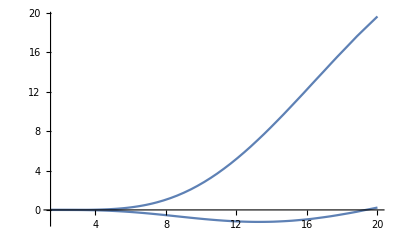

```mathematica
teukint = {r,θ}|->TeukolskyTintegrandExpl[r,θ]*Sin[θ]*PrivateTeukolsky`SWSHS[2][θ];
teukint[3.86,1]
teukint[20,2]
Plot[teukint[r,1]//ReIm, {r,1.45,20}]
```

Comparison of Tlmω

```mathematica
Tlmω[2][3.86]
Tlmω[2]
Plot[Tlmω[2][r]//ReIm, {r,1.44,100}]
```

0.0269771-0.0434657 ⅈ

Comparison of Renormalized angular momentum

```mathematica
TeuInterEnv`νsolIn[2,2][2*TeuInterEnv`wr]//Evaluate
RenormalizedAngularMomentum[-2,2,2,0.9`20.,SetPrecision[4*TeuInterEnv`wr,64],Method->"Monodromy"]
```

RenormalizedAngularMomentum[-2.,2.,2.,0.9,1.1345294414398515,Method→Monodromy]

Comparison of Homogeneous solution of MST

```mathematica
With[{TeuInterEnv`spinin=0.9,TeuInterEnv`wr=0.2836323604304887114412526546297144404`25.150514992000527,TeuInterEnv`rstop = 400},
Off[Power::infy];
MSTgRoots[TeuInterEnv`spinin,-2,2,2,2];
νsol[w_]:=nufullBHPT[w];
MSTSolution[TeuInterEnv`spinin,νsol[2*TeuInterEnv`wr],2*TeuInterEnv`wr,AlmSWSH[2*TeuInterEnv`wr], -2,2,2,TeuInterEnv`rstop];
rsol22 = MSTformalism`Rnumerical;
On[Power::infy];
]
```

λ_(swsh,  MSTpackage): 0.657813089546964

Comparison of Z_lmω integrand

```mathematica
tlmw = TeuInterEnv`Tlmω[2];
Rin = {TeuInterEnv`r}|->TeuInterEnv`RinSet[2,2]//Evaluate;
integrand = {r}|->tlmw[r]*Rin[r]/((r^2-2*r+(0.9)^2)^2);
Plot[integrand[r]//Abs, {r,1.45,100}];
integrand[3.86]
```

0.00114702+0.0666179 ⅈ

Comparison of incoming amplitude

```mathematica
TeuInterEnv`BincSet[2,2]
```

15.557757161322688703-1.268787801534708842 ⅈ

Comparison of Z_lmω

```mathematica
integration = NIntegrate[integrand[rr],{rr,2.5,TeuInterEnv`rstop},MaxRecursion->50,WorkingPrecision->10]
zinf = integration/(2 * I * 2*TeuInterEnv`wr * TeuInterEnv`BincSet[2,2])
```

-0.005698989892+0.00146165492 ⅈ

0.0000561051227+0.0003274510897 ⅈ

```mathematica
3
```